```mathematica
Quit[]
```

# initial conditions

```mathematica
(*User supplied data*)
(*data 1 *)
G=1;ϵ= 3/1000; spinSuppressFac = ϵ^(1/2);    c = 1/spinSuppressFac   ;
m1=1.5;m2=1; λ0=0;λmax=2;
Rinit={0.1,0.2,-1.5698814161627594};
Pinit={0.85,-0.3710678118654742,-0.149199868560037};

S1init={0,1/(√2),1/(√2)};
S2init={(√(3/2))/2,(√(3/2))/2,1/2};

(*data 2 *)
(*G=1;ϵ= 3/1000; spinSuppressFac = ϵ^(1/2);    c = 1/spinSuppressFac   ;
m1=1.5;m2=1; λ0=0;λmax=2;
Rinit={1,.5,1.5};
Pinit={1,-4,1};
S1init={1,1,1.3};
S2init={-7.5,-1.5,4.2};*)
(*end of user supplied  data*)

μ =m1  m2 /(m1+m2); M=m1+m2;
Q1=(2+3 m2/(2 m1));Q2=(2+3 m1/(2 m2));
zhat={0,0,1};
```

```mathematica
R={Rx[λ],Ry[λ],Rz[λ]};P={Px[λ],Py[λ],Pz[λ]};
S1={S1x[λ],S1y[λ],S1z[λ]};S2={S2x[λ],S2y[λ],S2z[λ]};
Seff= Q1 S1 + Q2 S2 ;
L = Cross[R,P] ;




eqa=D[R,λ]-(Cross[Seff,R]);
eqb=D[P,λ]-(Cross[Seff,P]);
eqc=D[S1,λ]-(Q1 Cross[L,S1]);
eqd=D[S2,λ]-(Q2 Cross[L,S2]);

system0={eqa[[1]]==0,eqa[[2]]==0,eqa[[3]]==0, eqb[[1]]==0,eqb[[2]]==0,eqb[[3]]==0,eqc[[1]]==0,eqc[[2]]==0,eqc[[3]]==0,eqd[[1]]==0,eqd[[2]]==0,eqd[[3]]==0}//Simplify;
initCond = {Rx[0] == Rinit[[1]], Ry[0] == Rinit[[2]], Rz[0] == Rinit[[3]], Px[0] == Pinit[[1]], Py[0] == Pinit[[2]], Pz[0] == Pinit[[3]] , S1x[0] ==S1init[[1]], S1y[0] == S1init[[2]], S1z[0] ==S1init[[3]], S2x[0] == S2init[[1]], S2y[0] == S2init[[2]], S2z[0] == S2init[[3]]}  ;
sol=NDSolve[   system0~Join~initCond  ,  {Rx, Ry, Rz, Px, Py,Pz,S1x, S1y, S1z,S2x, S2y, S2z},{λ,0,λmax}];
```

# Parametric plot of trajectory

```mathematica
ParametricPlot3D[Evaluate[{Rx[λ],Ry[λ],Rz[λ]}/. sol],{λ,0,λmax}]
```

-Graphics3D-

# More plots

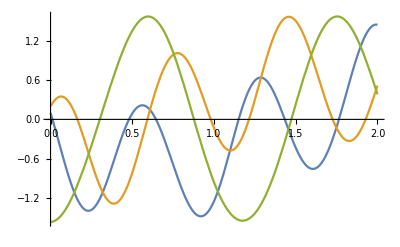

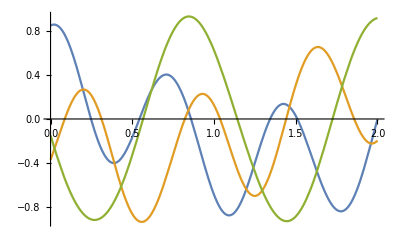

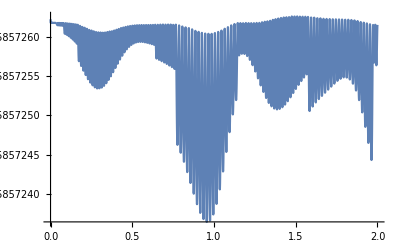

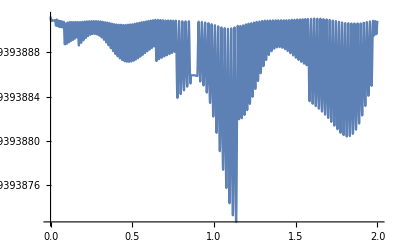

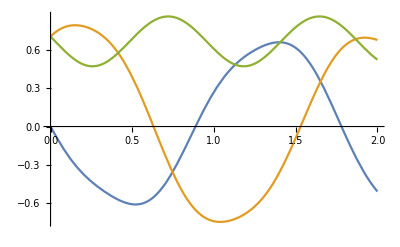

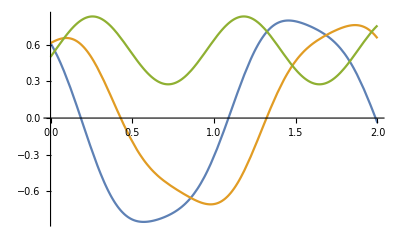

```mathematica
Plot[{Rx[λ]/.sol,Ry[λ]/.sol,Rz[λ]/.sol},{λ,0,λmax}]
Plot[{Px[λ]/.sol,Py[λ]/.sol,Pz[λ]/.sol},{λ,0,λmax},PlotRange->All]
Plot[Norm[{Rx[λ],Ry[λ],Rz[λ]}]/.sol,{λ,0,λmax}]
Plot[Norm[{Px[λ],Py[λ],Pz[λ]}]/.sol,{λ,0,λmax},PlotRange->All]
Plot[{S1x[λ]/.sol,S1y[λ]/.sol,S1z[λ]/.sol},{λ,0,λmax}]
Plot[{S2x[λ]/.sol,S2y[λ]/.sol,S2z[λ]/.sol},{λ,0,λmax}]
```

# evolution of S1.S2/ (Q1-Q2)

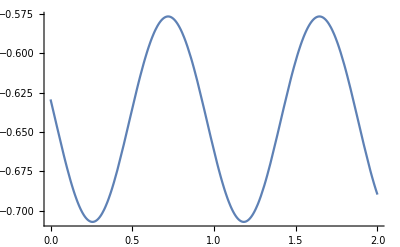

```mathematica
Plot[((S1.S2)/(Q1-Q2))/.sol,{λ,0,λmax}]
```

```mathematica
S1init.S2init/(Q1-Q2) (*check starting value*)
```

2.832

# evolution of ϕL

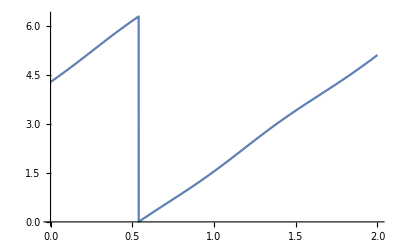

```mathematica
ϕL= ArcTan[(R × P)[[1]],(R × P)[[2]]];
Plot[Mod[ϕL/.sol,2π],{λ,0,λmax}]
```

# Evolution of ϕ

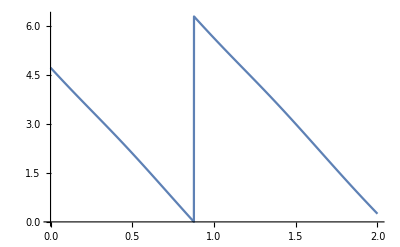

```mathematica
acos[k_,a_,b_]:= If[k.(a×b)>0,VectorAngle[a,b],2π-VectorAngle[a,b]];
acos[(R × P), (((R × P)+S1+S2) × (R × P)),R];

Plot[acos[(R × P), (((R × P)+S1+S2) × (R × P)),R]/.sol,{λ,0,λmax}]
```

# collecting some plots for comparison

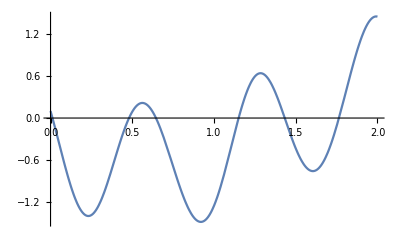

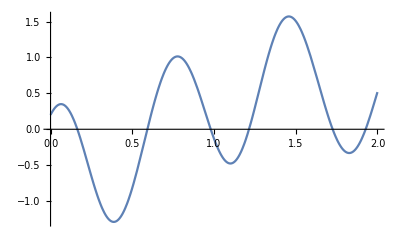

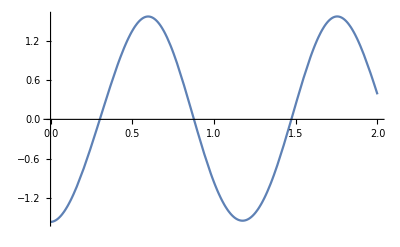

```mathematica
Plot[Rx[λ]/.sol,{λ,0,λmax}]
Plot[Ry[λ]/.sol,{λ,0,λmax}]
Plot[Rz[λ]/.sol,{λ,0,λmax}]
```

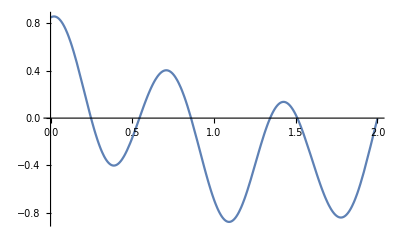

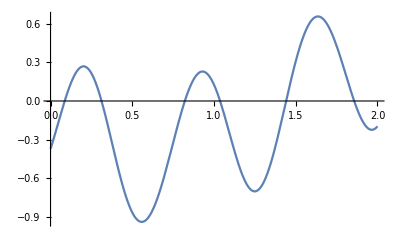

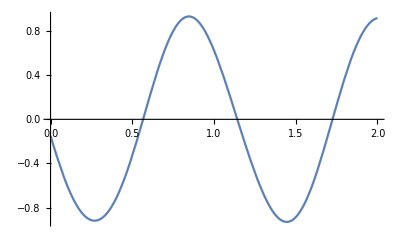

```mathematica
Plot[Px[λ]/.sol,{λ,0,λmax}]
Plot[Py[λ]/.sol,{λ,0,λmax}]
Plot[Pz[λ]/.sol,{λ,0,λmax}]
```

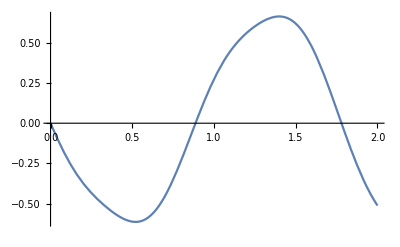

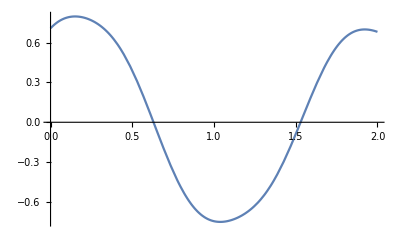

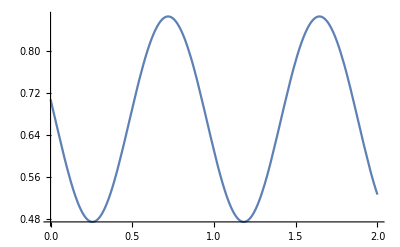

```mathematica
Plot[S1x[λ]/.sol,{λ,0,λmax}]
Plot[S1y[λ]/.sol,{λ,0,λmax}]
Plot[S1z[λ]/.sol,{λ,0,λmax}]
```

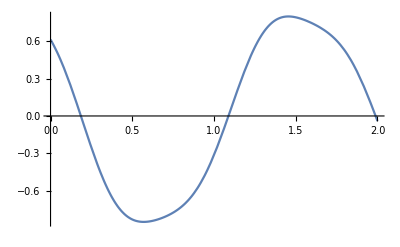

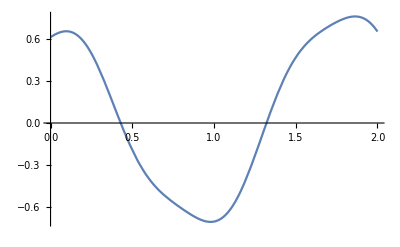

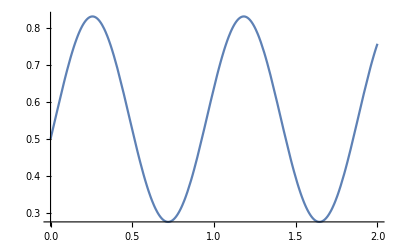

```mathematica
Plot[S2x[λ]/.sol,{λ,0,λmax}]
Plot[S2y[λ]/.sol,{λ,0,λmax}]
Plot[S2z[λ]/.sol,{λ,0,λmax}]
```

```mathematica
Show[Graphics3D[{{Blue,Arrowheads[0.03],Arrow[{{0,0,0},Rinit}]},{Green,Arrowheads[0.03],Arrow[{{0,0,0},Pinit}]},{Brown,Arrowheads[0.03],Arrow[{{0,0,0},S1init}]},{Magenta,Arrowheads[0.03],Arrow[{{0,0,0},S2init}]}}],ParametricPlot3D[Evaluate[{Rx[λ],Ry[λ],Rz[λ]}/. sol],{λ,λ0,λmax},PlotStyle->Blue],ParametricPlot3D[Evaluate[{Px[λ],Py[λ],Pz[λ]}/. sol],{λ,λ0,λmax},PlotStyle->Green],ParametricPlot3D[Evaluate[{S1x[λ],S1y[λ],S1z[λ]}/. sol],{λ,λ0,λmax},PlotStyle->Brown],ParametricPlot3D[Evaluate[{S2x[λ],S2y[λ],S2z[λ]}/. sol],{λ,λ0,λmax},PlotStyle->Magenta],Boxed->False]
```

-Graphics3D-